```mathematica
data = Import["~/Desktop/TripAdvisorChallenge/datathon_tadata.csv"];
```

```mathematica
dHeader = data[[1]];
```

```mathematica
dHeader
```

{user_id,day,gender,p_sessionActivity,p_AddToCart,p_trafficChannel,p_sessionDuration,p_pageViews,daysToCheckin,osType,osTypeName,daysFromPreviousVisit,p_TotalPrice,isExclusiveMember,loggedIn,p_MapInteraction,BookingPurchase}

```mathematica
Thread[data[[1]]->Range[1,17]]
```

{user_id→1,day→2,gender→3,p_sessionActivity→4,p_AddToCart→5,p_trafficChannel→6,p_sessionDuration→7,p_pageViews→8,daysToCheckin→9,osType→10,osTypeName→11,daysFromPreviousVisit→12,p_TotalPrice→13,isExclusiveMember→14,loggedIn→15,p_MapInteraction→16,BookingPurchase→17}

```mathematica
dSet[x_]:= data[[2;;,x]];
```

```mathematica
(* Indices of users who made booking *)
```

```mathematica
purch = dSet[17];
```

```mathematica
iPurch= DeleteCases[If[purch[[#]]==1,#]&/@Range[Length[purch]],Null];
```

```mathematica
iNotPurch = Complement[Range[Length[purch]],iPurch];
```

```mathematica
(* Determine the indices of those users who had NA in one of the specific fields *)
```

```mathematica
hasNA [x_]:=(#=="NA")&/@dSet[x];
```

```mathematica
removeNAIndex[x_] := DeleteCases[dSet[x],"NA"];
```

```mathematica
removeNAIndex[x_]:=Flatten[Position[dSet[x],"NA"]]
```

```mathematica
iNA[x_]:= Complement[Range[Length[dSet[x]]],removeNAIndex[x]];
```

```mathematica
removeNA[x_]:=dSet[x][[Complement[Range[Length[dSet[x]]],removeNAIndex[x]]]];
```

```mathematica
(* Split the data in purchase and not purchase sets *)
```

```mathematica
pData[x_] := dSet[x][[iPurch]];
nData[x_]:= dSet[x][[iNotPurch]];
```

```mathematica
tc2N=Thread[#->Range[Length[#]]]&@Union[dSet[6]];
```

```mathematica
tc2N
```

{A→1,B→2,C→3,D→4,H→5,O→6}

```mathematica
Union[dSet[10]]
```

{1,7,8,10,11,12,13,14,16}

```mathematica
(* LEGEND FOR NEW DATA *)
```

```mathematica
Thread[data[[1]][[{4,5,6,7,8,9,10,12,13,14,15,16,17}]]->Range[1,13]]
```

{p_sessionActivity→1,p_AddToCart→2,p_trafficChannel→3,p_sessionDuration→4,p_pageViews→5,daysToCheckin→6,osType→7,daysFromPreviousVisit→8,p_TotalPrice→9,isExclusiveMember→10,loggedIn→11,p_MapInteraction→12,BookingPurchase→13}

```mathematica
(* daysToCheckin: NA->7000, TotalPrice: NA->0, "A"->1,"B"->2,"C"->3,"D"->4,"H"->5,"O"->6 in p_trafficChannel  *)
```

```mathematica
newData = Transpose[{dSet[4],dSet[5],dSet[6]/.tc2N,dSet[7],dSet[8],dSet[9]/.{"NA"->7000},dSet[10],dSet[12],dSet[13]/.{"NA"->0},dSet[14],dSet[15],dSet[16],dSet[17]}];
```

```mathematica
newData[;;,6]
```

{{1,0,6,73,1,7000,8,10,0,0,0,0,0},{0,0,6,234,4,7000,7,42,0,0,0,0,0},{53,0,6,341,5,123,7,0,166,1,1,0,1},{0,0,6,778,1,7000,7,1,0,0,0,0,0},{0,0,6,34,1,7000,7,2,0,0,0,0,0},{1,0,1,375,1,7000,7,2,0,0,0,0,1},{39,0,1,825,20,7000,7,0,0,0,0,0,0},999986,{0,0,6,605,1,7000,7,7,0,0,0,0,0},{2,0,5,3410,3,16,7,2,0,0,1,0,1},{1,0,1,2,1,7000,8,16,0,0,0,0,0},{16,0,1,2983,5,83,7,1,1305,1,1,0,1},{0,0,6,4213,3,7000,7,49,0,0,0,0,0},{1,0,2,15,1,7000,10,1,0,0,0,0,1},{0,0,6,144,3,7000,7,0,0,0,0,0,1}}[1;;All,6]
 |  |  |  |

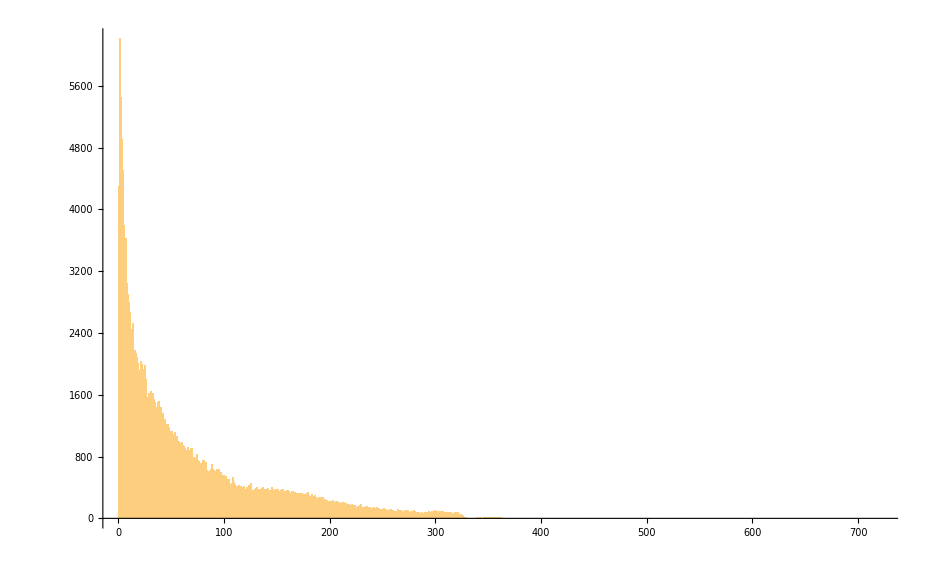

```mathematica
Histogram[dSet[9][[Complement[Range[Length[dSet[9]]],Flatten[Position[dSet[9]/.{"NA"->7000},7000]]]]],1000]
```

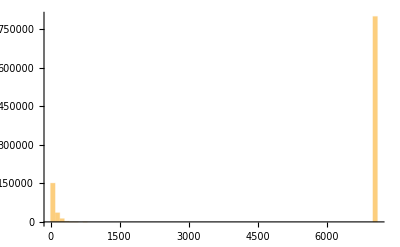

```mathematica
Histogram[dSet[9]/.{"NA"->7000},50]
```

```mathematica
class1[[11,1]]
```

98

```mathematica
(* Save the data in two different files for the two classes *)
```

```mathematica
(* Class 1 *)
```

```mathematica
class1=newData[[iPurch]];
```

```mathematica
Export["class1.csv",newData[[iPurch]]];
```

```mathematica
(* Class 0 *)
```

```mathematica
class0 = newData[[iNotPurch]];
```

```mathematica
Export["class0.csv",newData[[iNotPurch]]];
```

```mathematica
Dimensions[newData]
```

{1000000,13}

```mathematica
{dSet[9]/.{"NA"->7000},dSet[13]/.{"NA"->0}}
```

{{7000,7000,123,7000,7000,7000,7000,7000,7000,135,7000,7000,7000,7000,7000,24,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,1,7000,7000,7000,55,15,7000,7000,7000,0,7000,7000,14,7000,7000,7000,7000,119,7000,7000,7000,7000,7000,7000,7000,7000,25,999894,7000,292,7000,7000,13,47,7000,7000,7000,45,20,75,1,7000,40,7000,263,7000,7000,7000,7000,57,1,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,7000,8,5,7000,7000,7000,7000,7000,16,7000,83,7000,7000,7000},1}
 |  |  |  |

```mathematica
removeNAIndex[9]
```

{1,2,4,5,6,7,8,9,11,12,13,14,15,17,18,19,20,21,22,23,24,25,26,28,29,30,33,34,35,37,38,40,41,42,43,45,46,47,48,49,50,51,52,54,55,57,61,63,64,65,798718,999935,999936,999937,999938,999939,999940,999941,999942,999943,999944,999946,999947,999948,999950,999951,999954,999955,999956,999961,999963,999965,999966,999967,999968,999971,999972,999973,999974,999975,999976,999977,999978,999979,999980,999981,999982,999983,999984,999985,999986,999987,999990,999991,999992,999993,999994,999996,999998,999999,1000000}
 |  |  |  |

```mathematica
Max[removeNA[9]]
```

722

```mathematica
iPurch
```

{3,6,8,9,16,17,18,19,24,28,43,54,56,58,62,63,70,75,76,81,83,85,86,90,91,119,120,124,125,127,130,132,140,143,144,153,163,167,168,170,173,178,179,189,195,211,214,220,215245,999831,999833,999835,999837,999839,999843,999850,999853,999855,999857,999870,999876,999878,999879,999882,999891,999892,999893,999900,999903,999915,999920,999921,999922,999925,999927,999929,999933,999936,999939,999947,999948,999950,999953,999954,999955,999958,999962,999966,999968,999972,999984,999987,999995,999997,999999,1000000}
 |  |  |  |

```mathematica
iNotPurch
```

{1,2,4,5,7,10,11,12,13,14,15,20,21,22,23,25,26,27,29,30,31,32,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,49,50,51,52,53,55,57,59,60,61,64,65,66,784560,999931,999932,999934,999935,999937,999938,999940,999941,999942,999943,999944,999945,999946,999949,999951,999952,999956,999957,999959,999960,999961,999963,999964,999965,999967,999969,999970,999971,999973,999974,999975,999976,999977,999978,999979,999980,999981,999982,999983,999985,999986,999988,999989,999990,999991,999992,999993,999994,999996,999998}
 |  |  |  |

```mathematica
(* Playing with the idea of using a bernoulli distrib to model the maximum likelihood *)
```

```mathematica
mu1[x_]:=Total[#]/Length[#]&@pData[x]//N;
mu0[x_]:=Total[#]/Length[#]&@nData[x]//N;
```

```mathematica
mu0[#]&/@{14,15,16}
```

{0.135771,0.180037,0.00910713}

```mathematica
mu1[#]&/@{14,15,16}
```

{0.224334,0.27823,0.0108619}

```mathematica
b[mu_,x_]:= (mu^x)(1-mu)^(1-x);
```

```mathematica
p[muVector_,xVector_]:=Product[b[muVector[[i]],xVector[[i]]],{i,1,Length[muVector]}];
```

```mathematica
xVec [i_]:=  {dSet[14][[i]],dSet[15][[i]],dSet[16][[i]]};
```

```mathematica
p[%230,#]&@{dSet[14][[1]],dSet[15][[1]],dSet[16][[1]]}
```

0.702182

```mathematica
If[p[%230,xVec [1]]>p[%231,xVec [1]],0==dSet[17][[1]],1==dSet[17][[1]]]/@Range[Length[]]
```

True

```mathematica
If[p[%230,xVec [#]]>p[%231,xVec [#]],0==dSet[17][[#]],1==dSet[17][[1]]]&@1
```

True

```mathematica
If[p[%230,xVec [#]]>p[%231,xVec [#]],0==dSet[17][[#]],1==dSet[17][[1]]]&@13
```

True

```mathematica
If[p[%230,xVec [#]]>p[%231,xVec [#]],0==dSet[17][[#]],1==dSet[17][[#]]]&/@Range[200]
```

{True,True,True,True,True,False,True,False,False,False,True,True,True,True,True,True,False,False,True,True,True,True,True,False,True,True,False,False,True,True,False,False,True,True,True,False,True,True,False,True,True,True,True,False,True,True,True,True,True,True,True,True,False,False,True,True,True,True,False,False,True,True,False,True,True,True,True,True,True,False,True,True,False,False,True,True,True,False,True,True,False,True,False,True,False,False,True,False,True,False,False,True,True,False,True,False,False,False,True,True,True,True,False,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,False,False,True,True,True,False,False,True,False,True,True,False,False,False,True,True,True,True,True,True,True,False,True,True,False,True,True,False,True,True,False,True,True,True,True,True,True,True,False,True,True,True,True,True,False,True,True,True,False,False,False,True,True,True,False,True,True,True,False,False,False,True,True,True,True,True,True,True,True,False,False,True,False,True,False,True,False,True,False,True,True,False}

```mathematica
Length[Flatten[Position[%282,True]]]/200.
```

0.68

```mathematica
For[i=1,i≤Length[dSet[17]],set={};If[p[%230,xVec [#]]>p[%231,xVec [#]],AppendTo[set,0==dSet[17][[#]]],AppendTo[set,1==dSet[17][[#]]]]&@i]
```

$Aborted

```mathematica
p[%231,#]&@{dSet[14][[1]],dSet[15][[1]],dSet[16][[1]]}
```

0.553772

```mathematica
dSet[17][[1]]
```

0

```mathematica
nData[17][[1]]
```

0

```mathematica
mu[16]
```

0.0108619

```mathematica
mu1[16]
```

0.0108619

```mathematica
mu0[16]
```

0.00910713

```mathematica
mu[15]
```

0.27823

```mathematica
(* Correlations with NA removed; 9,13 *)
```

```mathematica
Correlation[removeNA[9],dSet[17][[iNA[9]]]]*1.0
```

0.0025571

```mathematica
SpearmanRho[removeNA[9],dSet[17][[iNA[9]]]]*1.0
```

0.0161099

```mathematica
Correlation[removeNA[13],dSet[17][[iNA[13]]]]*1.0
```

0.00264451

```mathematica
SpearmanRho[removeNA[13],dSet[17][[iNA[13]]]]*1.0
```

0.0238003

```mathematica
(* Relationships between variables *)
```

```mathematica
Correlation[dSet[5],dSet[17]]*1.0
```

0.0257137

```mathematica
SpearmanRho[dSet[5],dSet[17]]*1.0
```

0.0257137

```mathematica
Correlation[dSet[16],dSet[17]]*1.0
```

0.00744171

```mathematica
SpearmanRho[dSet[16],dSet[17]]*1.0
```

0.00744171

```mathematica
Correlation[dSet[15],dSet[17]]*1.0
```

0.100685

```mathematica
SpearmanRho[dSet[15],dSet[17]]*1.0
```

0.100685

```mathematica
Correlation[dSet[14],dSet[17]]*1.0
```

0.100633

```mathematica
Correlation[dSet[14],dSet[15]]*1.0
```

0.732738

```mathematica
SpearmanRho[dSet[14],dSet[15]]*1.0
```

0.732738

```mathematica
ListPlot[Transpose[{dSet[7],dSet[17]+1}]]
```

-Graphics-

```mathematica
(* Define functions to determine if two of the boolean fields are true for each user *)
```

```mathematica
bothTrue[x_,y_]:= (#[[1]]==#[[2]])&/@Transpose[{x,y}];
```

```mathematica
bookedAndExclusiveMember = bothTrue[dSet[14],dSet[17]];
```

```mathematica
ExclusiveMemberAndLoggedIn= bothTrue[dSet[14],dSet[15]];
```

```mathematica
ExclusiveMemberAndLoggedIn/.{True->1,False->0}
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,999881,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1}
 |  |  |  |

```mathematica
(bookedAndExclusiveMember/.{True->1,False->0})+(ExclusiveMemberAndLoggedIn/.{True->1,False->0})
```

{2,2,2,2,2,1,2,1,1,1,2,2,2,2,2,0,1,1,1,2,2,2,2,1,2,2,1,1,2,2,1,1,2,2,2,1,2,2,1,2,2,2,1,1,2,2,2,2,2,2,2,2,1,1,2,2,2,2,1,1,2,2,1,2,2,2,2,2,2,1,2,2,1,1,2,2,2,1,2,2,1,2,1,2,1,1,2,0,2,1,1,2,2,1,2,1,1,1,2,2,2,2,1,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,1,1,2,2,2,1,999752,2,1,1,2,1,2,1,2,2,2,2,1,2,2,1,1,1,2,2,2,2,2,1,1,2,2,2,1,2,2,1,2,1,2,2,2,2,2,1,2,2,2,2,1,1,1,2,2,1,2,1,2,1,2,2,2,1,2,2,1,2,2,1,2,2,2,2,2,1,2,1,1,1,1,2,1,2,1,1,2,1,0,1,1,2,2,2,1,2,1,2,1,1,1,2,1,2,2,2,2,0,2,2,2,2,2,2,1,2,2,1,1,1,2,2,2,2,2,0,2,2,2,1,1}
 |  |  |  |

```mathematica
Maximize[Correlation[x*dSet[14]+y*dSet[15]+z*dSet[16],dSet[17]]*1.0,{x,y,z}]
```

$Aborted

```mathematica
Maximize
```

```mathematica
Correlation[dSet[14]+dSet[15]+dSet[16],dSet[17]]*1.0
```

```mathematica
Correlation[%196,dSet[17]]*1.0
```

-0.507656

```mathematica
Correlation[bookedAndExclusiveMember/.{True->1,False->0},ExclusiveMemberAndLoggedIn/.{True->1,False->0}]*1.0
```

0.056024

```mathematica
dSet[9][[1]]
```

NA

```mathematica
dSet[4]//Length
```

1000000

```mathematica
dSet[17]//Length
```

1000000

```mathematica
ListPlot[Transpose[{dSet[17],dSet[4]}]]
```

-Graphics-

```mathematica
nLoggedOut = Count[dSet[15],0];
```

```mathematica
nLoggedIn =Count[dSet[15],1];
```

```mathematica
Count[dSet[15],dSet[9][[1]]]
```

0

```mathematica
Count[dSet[9],dSet[9][[1]]]
```

798818

```mathematica
Dimensions[data]
```

{1000001,17}

```mathematica
(* Looking at the OS data fields *)
```

```mathematica
os2Label = Thread[#->Range[Length[#]]]&@DeleteDuplicates[dSet[11]]
```

{osx→1,windows→2,ipad_browser→3,android_tablet_browser→4,other→5,linux→6,ipad_hybrid_app→7,other_tablet→8,android_browser→9}

```mathematica
osCount = Thread[(First/@os2Label)->(Count[dSet[11],#]&/@( First/@os2Label))]
```

{osx→208973,windows→516192,ipad_browser→208455,android_tablet_browser→52529,other→11298,linux→1954,ipad_hybrid_app→293,other_tablet→275,android_browser→31}

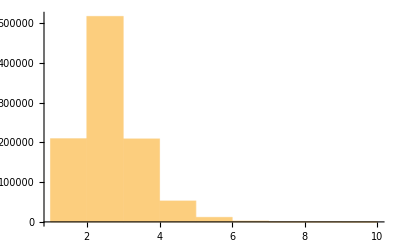

```mathematica
Histogram[dSet[11]/.os2Label]
```

```mathematica
dHeader[[11]]
```

osTypeName

```mathematica
dSet[11][[10000]]
```

osx

```mathematica
nBookers = Total[dSet[17]];
```

```mathematica
(* Some of the samples accuracies after training a nn in tensorFlow *)
```

```mathematica
{98.6716,82.8274,76.322594,92.560402,94.9618,95.079201,73.7556,97.676399,77.890198,81.020401,82.400803,83.321602,79.041603,81.805405,94.7966,82.023796,97.128204,94.619202,87.906197,81.683998,80.994598,77.939598,82.205406,80.965004,80.883995}
```

```mathematica
sampls={98.6716,82.8274,76.322594,92.560402,94.9618,95.079201,73.7556,97.676399,77.890198,81.020401,82.400803,83.321602,79.041603,81.805405,94.7966,82.023796,97.128204,94.619202,87.906197,81.683998,80.994598,77.939598,82.205406,80.965004,80.883995};
```

```mathematica
Mean[sampls]
```

85.5393

```mathematica
?MeanDeviation
```

```mathematica
MeanDeviation[sampls]
```

6.6837

```mathematica
StandardDeviation[sampls]
```

7.63016